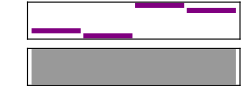

```mathematica
Sound[{SoundNote["E"],SoundNote["D#"],SoundNote["A"],SoundNote["G#"]}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
tune=Flatten[Table[{"A"<>ToString[n]->"G#"<>ToString[n],
"E"<>ToString[n]->"D#"<>ToString[n]},{n,1,9}]];
Tune[name_]:=(sn=Import[name<>".mid"]/.tune;Export[name<>"-l.mid",sn];sn)
Tune[name_,rule_]:=(sn=Import[name<>".mid"]/.tune/.rule;Export[name<>"-l.mid",sn];sn)
```

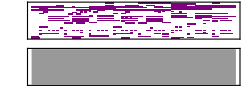

```mathematica
Tune["生日快乐歌"]
```

```mathematica
Tune["小星星变奏"]
```

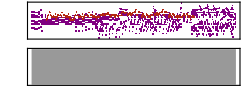

```mathematica
Tune["幻化成风","Voice"->"Harmonica"]
```

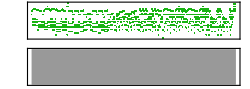

```mathematica
Tune["secret base","Piano"->"NewAge"]
```

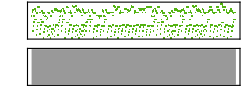

```mathematica
Tune["青春修炼手册","Piano"->"Harp"]
```